```mathematica
GP[r_]:=(1-L^2/r^2) G[r]-G[r]^3+G'[r]/r+G''[r]==0;
```

```mathematica
Ansatz={G[r]-> A+r^-β,G'[r]-> D[A+r^-β,r],G''[r]-> D[A+r^-β,{r,2}]}
```

{G[r]→A+r^-β,G'[r]→-r^(-1-β) β,G''[r]→-r^(-2-β) (-1-β) β}

```mathematica
Ansatz0={G[r]->r^β,G'[r]-> D[r^β,r],G''[r]-> D[r^β,{r,2}]}
```

{G[r]→r^β,G'[r]→r^(-1+β) β,G''[r]→r^(-2+β) (-1+β) β}

```mathematica
Series[GP[r]/.Ansatz0,{r,0,1},Assumptions-> β>0]//Normal//FullSimplify
```

r^(-2+β) (r^2+β^2)==r^(3 β)

```mathematica
0==0/.β->L
```

```mathematica
r^(1+3 L)==0
```

```mathematica
Series[GP[r]/.Ansatz,{r,∞,2},Assumptions-> β>0]/.A->0//Normal//FullSimplify
```

r^(-1+β) (r^2+β^2)==r^(1-β)

```mathematica
rInf=0.01;L=1;
```

```mathematica
GP[r_]:=(1-L^2/r^2) G[r]-G[r]^3+G'[r]/r+G''[r]==0;
```

```mathematica
sol=NDSolve[{GP[r],G'[rInf]==L, G[rInf]==0},{G},{r,rInf,7}]
```

{{G→InterpolatingFunction[…]}}

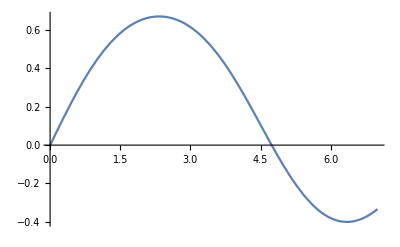

```mathematica
Plot[G[r]/.sol,{r,rInf,7}]
```

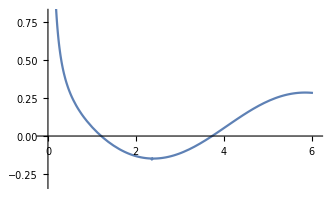

```mathematica
DSolve[(1-L^2/r^2) G[r]-G[r]^3+G'[r]/r+G''[r]==0,G[r],r]
```

DSolve[(1-4/r^2) G[r]-G[r]^3+G'[r]/r+G''[r]==0,G[r],r]